```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/Critical-region/QCD/v1/Tpc/msigma

```mathematica
l=40;
mi=1;
me=63;
T=Table[Flatten[Table[Import["./mpi_"<>ToString[j]<>"/Tem"<>ToString[i]<>"/BUFFER/T.DAT",SetPrecision->20],{i,1,l}]],{j,mi,me}];
(*sigma=Table[Flatten[Table[Import["./mpi_"<>ToString[j]<>"/Tem"<>ToString[i]<>"/BUFFER/FPI.DAT",SetPrecision->15],{i,1,l}]],{j,mi,me}];*)
ms=Table[Flatten[Table[Import["./mpi_"<>ToString[j]<>"/Tem"<>ToString[i]<>"/BUFFER/MSIGMA.DAT",SetPrecision->20],{i,1,l}]],{j,mi,me}];
(*z=Table[Flatten[Table[Import["./mpi_"<>ToString[j]<>"/Tem"<>ToString[i]<>"/BUFFER/ZPHI.DAT",SetPrecision->15],{i,1,l}]],{j,mi,me}];*)
```

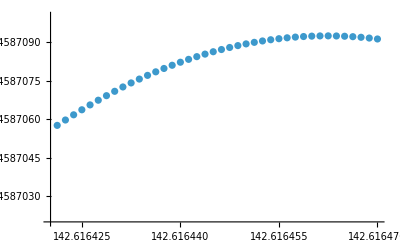

```mathematica
ListPlot[Table[Transpose[{T[[i]],1./(ms[[i]])}],{i,me,me}],PlotRange->{All,{0.7458702,0.745871}}]
```

```mathematica
(*ListPlot[Table[Transpose[{T[[i]],sigma[[i]]}],{i,mi,me}],ScalingFunctions->{"Log",Automatic},PlotRange->{All,All}]*)
```

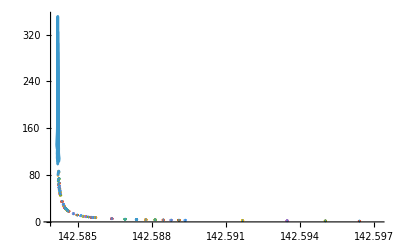

```mathematica
fit=Table[Interpolation[Transpose[{T[[i]],1/ms[[i]]}],InterpolationOrder->3],{i,1,me}];
Show[ListPlot[Table[Transpose[{T[[i]],1/ms[[i]]}],{i,1,me}]],Table[Plot[fit[[i]][x],{x,T[[i]][[1]],T[[i]][[40]]}],{i,1,me}]]
```

```mathematica
Tpc=Table[FindMaximum[fit[[i]][x],{x,T[[i]][[20]],T[[i]][[5]],T[[i]][[35]]},WorkingPrecision->25,AccuracyGoal->17,PrecisionGoal->17][[2]][[1]][[2]],{i,1,me}];
```

FindMaximum::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使函数的值增大得足够多. 您可能需要多于 25. 位的工作精度以满足这些容差.

General::stop: 在本次计算中，FindMaximum::lstol 的进一步输出将被抑制.

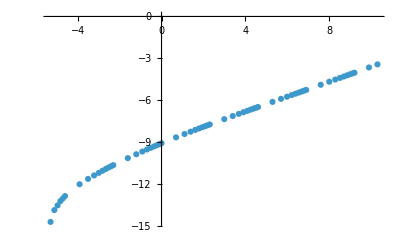

```mathematica
cl={4*10^-3,5*10^-3,6*10^-3,7*10^-3,8*10^-3,9*10^-3,1*10^-2,2*10^-2,3*10^-2,4*10^-2,5*10^-2,6*10^-2,7*10^-2,8*10^-2,9*10^-2,1*10^-1,2*10^-1,3*10^-1,4*10^-1,5*10^-1,6*10^-1,7*10^-1,8*10^-1,9*10^-1,1,2,3,4,5,6,7,8,9,10,20,30,40,50,60,70,80,90,100,200,300,400,500,600,700,800,900,1000,2000,3000,4000,5000,6000,7000,8000,9000,10^4,2*10^4,3*10^4};
ListPlot[Transpose[{Log[cl[[2;;me]]],Log[Tpc[[2;;me]]-Tpc[[1]]]}],PlotRange->{All,All}]
```

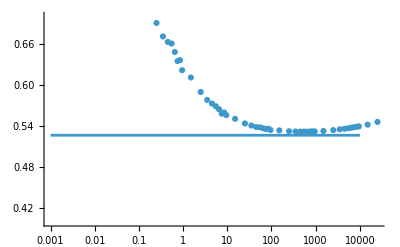

```mathematica
fitscale=Table[{(cl[[i+1]]+cl[[i]])/2.,FindFit[Transpose[{Log[cl[[i;;i+1]]],Log[Tpc[[i;;i+1]]-Tpc[[1]]]}],a+b x,{a,b},x][[2]][[2]]},{i,2,me-1}];
Show[ListPlot[fitscale,ScalingFunctions->{"Log",Automatic}],ListLinePlot[{{0.001,1./(0.397*4.784)},{10000,1./(0.397*4.784)}},ScalingFunctions->{"Log",Automatic}],PlotRange->{All,{0.4,0.7}}]
```

```mathematica
clall={4.*10^-3,5.*10^-3,6.*10^-3,7.*10^-3,8.*10^-3,9.*10^-3,1.*10^-2,2.*10^-2,3.*10^-2,4.*10^-2,5.*10^-2,6.*10^-2,7.*10^-2,8.*10^-2,9.*10^-2,1.*10^-1,2.*10^-1,3.*10^-1,4.*10^-1,5.*10^-1,6.*10^-1,7.*10^-1,8.*10^-1,9.*10^-1,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,200.,300.,400.,500.,600.,700.,800.,900.,1000.,2000.,3000.,4000.,5000.,6000.,7000.,8000.,9000.,1.*10^4,2.*10^4,3.*10^4,4.*10^4,5.*10^4,6.*10^4,7.*10^4,8.*10^4,9.*10^4};
```

```mathematica
Export["cl.dat",clall]
```

cl.dat

```mathematica
Length[clall]
```

69

```mathematica
142.61001-142.60191
```

0.0081

```mathematica
142.61001+0.008
```

142.618